```mathematica
Get["C:\\Users\\HP\\Documents\\faks\\3. letnik\\5. semester\\NRO\\mathematica\\DN2\\montecarlopi.nb"];
```

```mathematica
n=10000;
monteCarloPi[n];
```

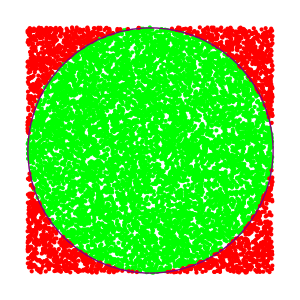

```mathematica
points=RandomReal[{-1,1},{n,2}];
insideCircle=Select[points,Norm[#]<=1&];
outsideCircle=Complement[points,insideCircle];

Graphics[{Thin,Green, Point[insideCircle],Thin,Red, Point[outsideCircle],Thick, Purple, Circle[{0,0},1]},AspectRatio->1,ImageSize->300]
```

```mathematica
Manipulate[Module[{approxPi,points,insideCircle,outsideCircle},approxPi=monteCarloPi[n];
points=RandomReal[{-1,1},{n,2}];
insideCircle=Select[points,Norm[#]<=1&];
outsideCircle=Complement[points,insideCircle];
Graphics[{Thin,Green, Point[insideCircle],Thin,Red, Point[outsideCircle],Thick, Purple, Circle[{0,0},1]},AspectRatio->1,ImageSize->300]],{{n,1000,"Število točk"},100,10000,100}]
```